# Plotting Density of State

```mathematica
Seq[e_,ϵ_,x_,y_]:=ϵ/((e-2Cos[x]-2Cos[y])^2+ϵ^2);(*This function defines the Dirac function sequence assuming chemical potential μ=0 and lattice constant a=1*)
```

```mathematica
DOS[ϵ_,m_,l_]:=Module[{},g=Table[{e,NIntegrate[Seq[e,ϵ,x,y],{x,-Pi,Pi},{y,-Pi,Pi},MaxRecursion->20,AccuracyGoal->5]},{e,-l,l,m}];ListPlot[g,PlotRange->All, AxesLabel->{"ϵ","DOS"},Joined->True]];
(*This function generates a table list using numerical integration and the associating listplot*)
```

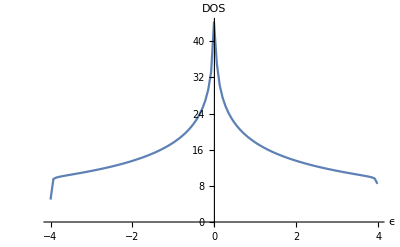

```mathematica
DOS[0.01,0.07,4]
```

```mathematica
(*Some message about the numerics issue may appear during the computation, but it works.*)
```